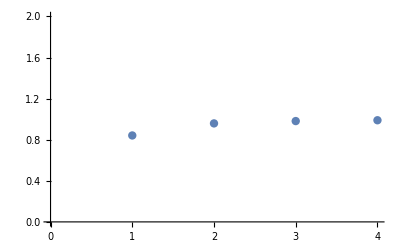

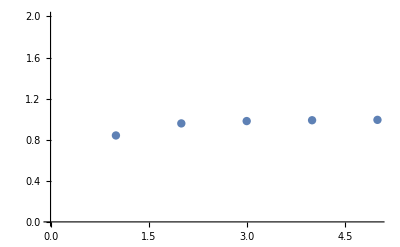

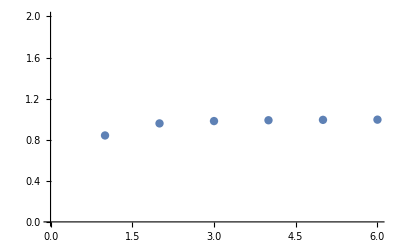

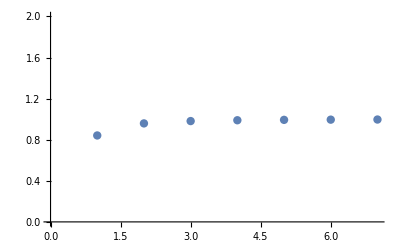

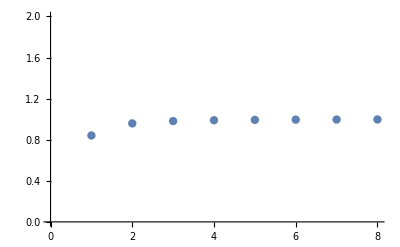

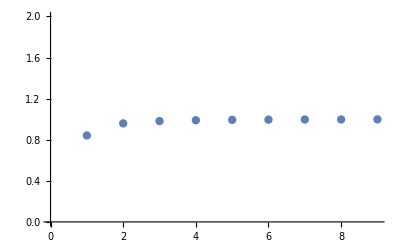

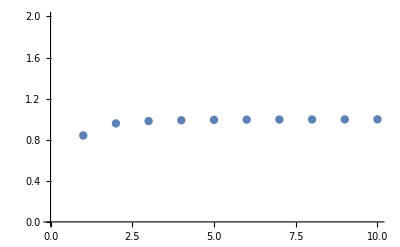

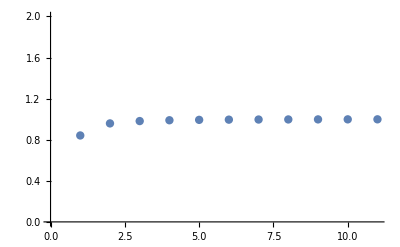

```mathematica
an ={Sin[1],2Sin[1/2],3Sin[1/3]};
Do[an=Append[an,i*Sin[1/i]];
t=ListPlot[an,PlotRange->{0,2},
PlotStyle->PointSize[0.015]];Print[t],{i,4,20}
]
```